## Single Pendulum

```mathematica
l = 1; tmax = 20; g = 9.8; w = l/g;
```

```mathematica
SinglePendulum[w_, pDot0_, tmax_] := s =  NDSolve[{Sin[p[t]]+ w p''[t]==0, p[0]==0, p'[0]== pDot0}, p, {t, 0, tmax}];
```

```mathematica
th :=  SinglePendulum[w,6.2608999, tmax]
```

```mathematica
s = p[t] /. th
```

{InterpolatingFunction[{{0., 20.}}, <>][t]}

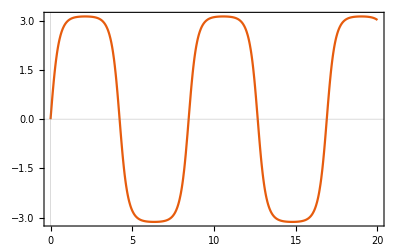

```mathematica
Plot[s,{t,0,tmax},PlotTheme->"Scientific",PlotRange->All]
```

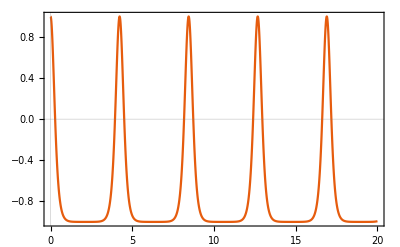

```mathematica
Plot[l Cos[s],{t,0,tmax},PlotTheme->"Scientific"]
```

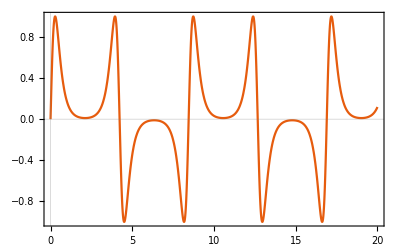

```mathematica
Plot[1 Sin[s],{t,0,tmax},PlotTheme->"Scientific"]
```